{x_1→ParametricFunction[<>],x_2→ParametricFunction[<>],p_1→ParametricFunction[<>]}

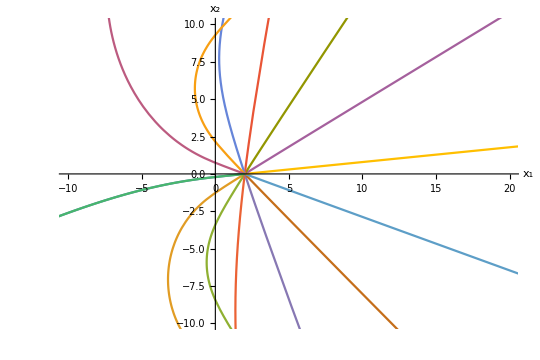

-Graphics3D-

```mathematica
SubMinus[c] = 6000.;
SubPlus[c]  = 1500;
SubMinus[ρ] = 3100.;
SubPlus[ρ] = 1000.;
ω = 2100.;

a = (SubMinus[ρ]/SubPlus[ρ])^2;
b = (SubPlus[c]/SubMinus[c])^2;
L0 = 0.;
p0 =√((ω^2 + L0)/SubPlus[c]^2) ;

minval = 2.5;
dmin = √(minval / p0^2(1 - b)) + Pi/2;
d[x1_] := ArcTan[x1] + dmin;
x1in = 2.;
x2in = 0.;
timeto = 1.0;

q = t /.FindRoot[{t^2 (a*(Cot[t])^2 + 1) == (d[x1in])^2 p0^2(1 - b)}, {t, 3.1}];
Subscript[p, abs] = Sqrt[p0^2 - (q/d[x1in])^2];

{x1sol, x2sol,p1sol} =ParametricNDSolve[{Subscript[x, 1]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[d[Subscript[x, 1][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))]/((Sin[d[Subscript[x, 1][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))])^3) 1/(√(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))) d[Subscript[x, 1][t]]- 2  (p0^2 (1/b - 1))/((p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))^2)) Subscript[p, 1][t],
Subscript[x, 2]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[d[Subscript[x, 1][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))]/((Sin[d[Subscript[x, 1][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))])^3) 1/(√(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))) d[Subscript[x, 1][t]] - 2  (p0^2 (1/b - 1))/((p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))^2))Subscript[p, abs] Sin[θ],
Subscript[p, 1]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[d[Subscript[x, 1][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))]/((Sin[d[Subscript[x, 1][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2))])^3) √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, abs] Sin[θ])^2)) 1/(1 + (Subscript[x, 1][t])^2)),                                             
Subscript[x, 1][0]==x1in, Subscript[x, 2][0]==x2in, Subscript[p, 1][0]==Subscript[p, abs] Cos[θ]},
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1]},{t,0.,timeto},{θ}]


ParametricPlot[Evaluate@Table[{(Subscript[x, 1][θ]/.x1sol)[t], (Subscript[x, 2][θ]/.x2sol)[t]}, {θ, 0.1, 2Pi + 0.1, Pi/7}], {t, 0. ,timeto}, PlotRange->{{-10.0, 20.},{-10., 10.}}, 
AxesLabel->{Subscript[x, 1], Subscript[x, 2]}]
Plot3D[d[x1], {x1, -10., 10.}, {x2, -10., 10.}, ColorFunction->(ColorData["TemperatureMap"][#3]&), Ticks->None]
```